# Pr^(3+):LaF_3 & Tm:LaF_3

```mathematica
AppendTo[$Path,NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];
Get["qlanth.m"]
```

## Tm^(3+)

```mathematica
spinspin=True;
numE=12;
TabulateManyEnergyMatrixTables[{1,2},{0},"Overwrite"->True,"ChenDeltas"->False];
{rmsDifferenceWithoutChenDeltas,gtEnergiesWithoutChenDeltas,cfenergiesWithoutChenDeltas,ln,carnallAssignments,{fstates,basis,symbolicMatrix}}=IonSolverLaF3[numE,"Include Spin-Spin"->spinspin];
without=cfenergiesWithoutChenDeltas-gtEnergiesWithoutChenDeltas;
params=LoadParameters["Tm","Free Ion"->False]
```

Symbols not in given params: {B12,B14,B16,B34,B36,B56,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T12,T14,T15,T16,T17,T18,T19,ϵ}

<|F2→100134.,F4→69613.,F6→55975.,ζ→2636.,α→17.26,β→-624.5,γ→1820.,T2→400.,T3→0.,T4→0.,T6→0.,T7→0.,T8→0.,M0→3.81,P2→695.,B02→-249.,B04→457.,B06→282.,B22→-105.,B24→320.,B44→428.,B26→-482.,B46→-234.,B66→-492.,n→56.,σ→10.,nf→12,F0→0,M2→2.1336,M4→1.1811,P0→0,P4→347.5,P6→69.5,gs→2.00232,gI→0.987,E0→0,E1→6793.51,E2→34.0549,E3→638.938|>

```mathematica
freeIonReps=(#[[1]]->#[[2]])&/@Transpose[{cfSymbols,ConstantArray[0,Length[cfSymbols]]}];
(*noMag={M0->0,M2->0,M4->0,P2->0,P4->0,P6->0};*)
noMag={};
freeIonReps=Join[freeIonReps,noMag];
freeHam=ReplaceInSparseArray[symbolicMatrix,freeIonReps];
tmParams=Carnall["data"]["Tm"];
tmParams=Select[tmParams,Not[#[[1]]===ζ]&];
simplifier={B12->0,B14->0,B16->0,B34->0,B36->0,B56->0,S12->0,S14->0,S16->0,S22->0,S24->0,S26->0,S34->0,S36->0,S44->0,S46->0,S56->0,S66->0,T11->0,T12->0,T14->0,T15->0,T16->0,T18->0,T17->0,T19->0};
eTofs=(#[[1]]->#[[2]])&/@Transpose[{{E0,E1,E2,E3},FtoE[F0,F2,F4,F6]}];
freeHam=Normal[freeHam]/. eTofs;
freeHam=freeHam/. simplifier;
freeHam=freeHam/.tmParams;
```

```mathematica
labels=First/@Carnall["appendix:"<>ln<>":RawTable"];
ulabels=DeleteDuplicates[labels];
palette=Table[ColorData["Rainbow",i],{i,0,1,1/(Length[ulabels]-1)}];
ulabels=(#[[1]]->#[[2]])&/@Transpose[{RandomSample[ulabels],palette}];
ulabels=Association[ulabels];
```

```mathematica
DeleteDuplicates[freeHam[[66;;78,66;;78]]//Diagonal]/.{σSS->1}
```

{666.928+14/13 (-8734.52+F0)+(41 M2)/132+(12865 M4)/18876+(635 P4)/26136-(875 P6)/339768+(5 ζ)/2}

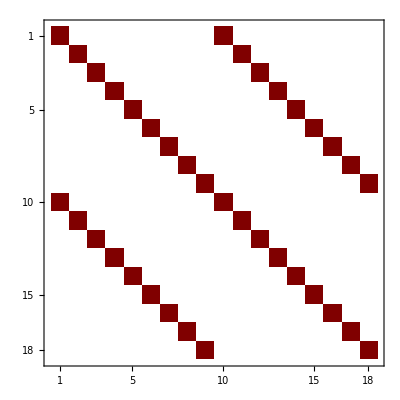

```mathematica
subBlock3H5=freeHam[[28;;45,28;;45]];
subBlock3H5=subBlock3H5/.{σSS->1,E0->0,E1->0,E3->0,α->0,β->0,γ->0,ζ->0};
MatrixPlot[subBlock3H5]
```

```mathematica
DeleteDuplicates[subBlock3H5//Diagonal]
```

{6372.48+14/13 (-8734.52+F0)+(19 M2)/36-(1285 M4)/396+(5 P4)/792+(175 P6)/10296,672.462+14/13 (-8734.52+F0)-(6353 M2)/990-(5369 M4)/2178-(127 P4)/4356+(175 P6)/56628}

```mathematica
Print["(*3F4 - 3H6*)"]
freeHam[[28,28]]-freeHam[[66,66]]
Print["(*3H5 - 3H6*)"]
freeHam[[55,55]]-freeHam[[66,66]]
Print["(*3H4 - 3H6*)"]
freeHam[[37,37]]-freeHam[[66,66]]
Print["(*3F3 - 3H6*)"]
freeHam[[21,21]]-freeHam[[66,66]]
```

(*3F4 - 3H6*)

5708.94-(239 M2)/66-(325 M4)/726-(235 P4)/13068+(3325 P6)/169884-ζ-3.38667 σSS+(380 M2 σSS)/99-(49250 M4 σSS)/14157

(*3H5 - 3H6*)

2.00256-(313 M2)/110-(361 M4)/242-(127 P4)/4356+(175 P6)/56628-3 ζ-9.144 σSS+(408 M2 σSS)/55+(3180 M4 σSS)/1573

(*3H4 - 3H6*)

3.67135-(313 M2)/60-(361 M4)/132-(127 P4)/2376+(175 P6)/30888-(11 ζ)/2+1.86267 σSS-(68 M2 σSS)/45-(530 M4 σSS)/1287

(*3F3 - 3H6*)

5768.6-(43 M2)/22-(365 M4)/242-(115 P4)/4356-(175 P6)/56628-3 ζ-(36 M2 σSS)/11+(19950 M4 σSS)/1573

```mathematica
TableForm[Transpose[{Range[Length[basis]],#[[1,1]]&/@basis}]]
```

1 | 3P
0
2 | 1S
0
3 | 3P
1
4 | 3P
1
5 | 3P
1
6 | 3P
2
7 | 3P
2
8 | 3P
2
9 | 3P
2
10 | 3P
2
11 | 3F
2
12 | 3F
2
13 | 3F
2
14 | 3F
2
15 | 3F
2
16 | 1D
2
17 | 1D
2
18 | 1D
2
19 | 1D
2
20 | 1D
2
21 | 3F
3
22 | 3F
3
23 | 3F
3
24 | 3F
3
25 | 3F
3
26 | 3F
3
27 | 3F
3
28 | 3F
4
29 | 3F
4
30 | 3F
4
31 | 3F
4
32 | 3F
4
33 | 3F
4
34 | 3F
4
35 | 3F
4
36 | 3F
4
37 | 3H
4
38 | 3H
4
39 | 3H
4
40 | 3H
4
41 | 3H
4
42 | 3H
4
43 | 3H
4
44 | 3H
4
45 | 3H
4
46 | 1G
4
47 | 1G
4
48 | 1G
4
49 | 1G
4
50 | 1G
4
51 | 1G
4
52 | 1G
4
53 | 1G
4
54 | 1G
4
55 | 3H
5
56 | 3H
5
57 | 3H
5
58 | 3H
5
59 | 3H
5
60 | 3H
5
61 | 3H
5
62 | 3H
5
63 | 3H
5
64 | 3H
5
65 | 3H
5
66 | 3H
6
67 | 3H
6
68 | 3H
6
69 | 3H
6
70 | 3H
6
71 | 3H
6
72 | 3H
6
73 | 3H
6
74 | 3H
6
75 | 3H
6
76 | 3H
6
77 | 3H
6
78 | 3H
6
79 | 1I
6
80 | 1I
6
81 | 1I
6
82 | 1I
6
83 | 1I
6
84 | 1I
6
85 | 1I
6
86 | 1I
6
87 | 1I
6
88 | 1I
6
89 | 1I
6
90 | 1I
6
91 | 1I
6

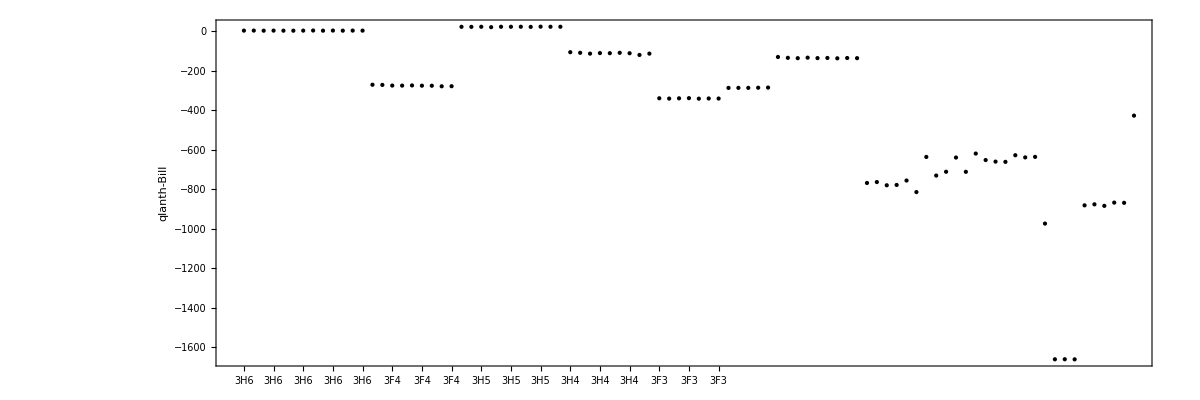

```mathematica
ListPlot[without,
Frame->True,
FrameLabel->{None,"qlanth-Bill"},
FrameTicks->{Transpose[{Range[Length[without]],Style[Rotate[#,Pi/2],ulabels[#]]&/@labels}], Automatic},
ImageSize->1200,
FrameStyle->Directive[12],
AspectRatio->1/3,
PlotStyle->{Black,PointSize[Medium]}]
```

```mathematica
terms=DeleteDuplicates[labels];
counters=Table[Count[labels,term],{term,terms}];
cuts=Prepend[Accumulate[counters],0];
```

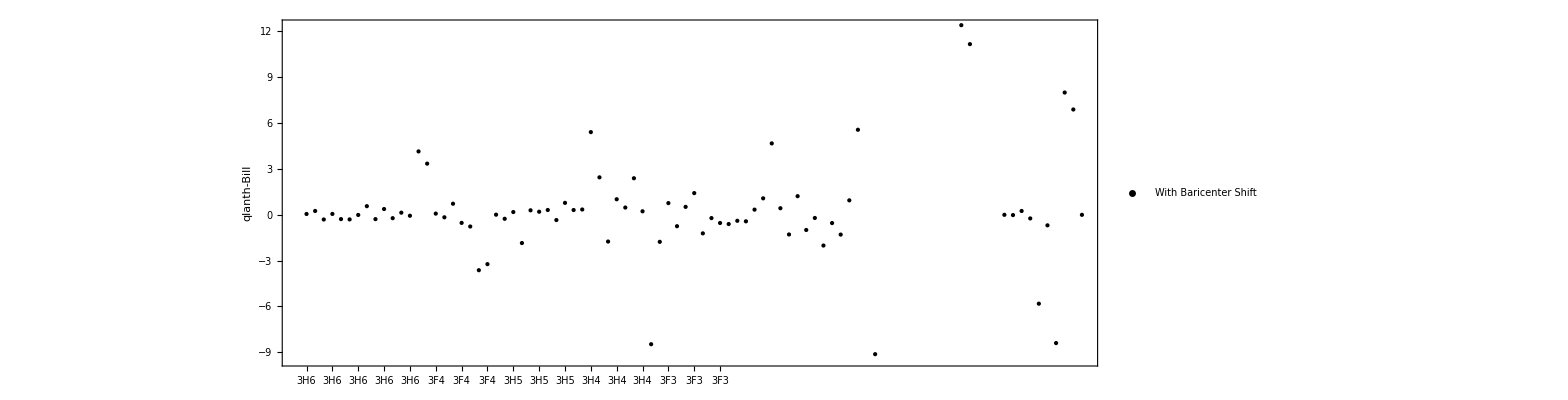

```mathematica
labelShifts={};
shifted=Table[(group=with[[cuts[[i]]+1;;cuts[[i+1]]]];
labelShifts=Append[labelShifts,Mean[group]];
group=group-Mean[group]
),{i,1,Length[cuts]-1}];
shifted=Flatten[shifted];
ListPlot[shifted,
PlotLegends->{"With Baricenter Shift"},
Frame->True,
FrameLabel->{None,"qlanth-Bill"},
FrameTicks->{Transpose[{Range[Length[with]],Style[Rotate[#,Pi/2],ulabels[#]]&/@labels}], Automatic},
ImageSize->1200,
FrameStyle->Directive[12],
AspectRatio->1/3,
PlotStyle->{Black,PointSize[Medium]}]
```

### With and Without Chen' s Errors

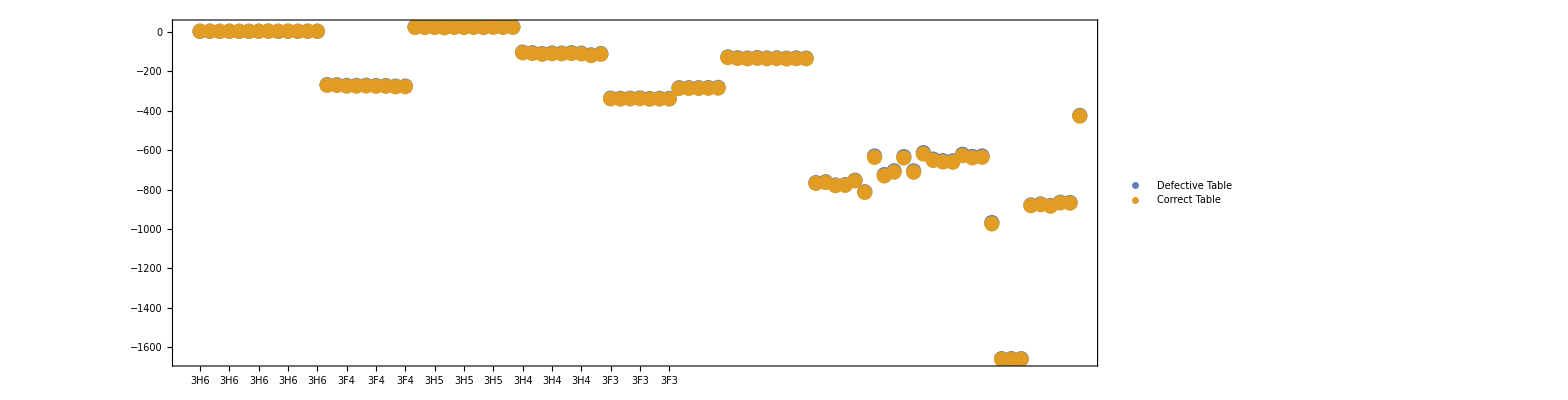

```mathematica
spinspin=True;
numE=12;
TabulateManyEnergyMatrixTables[{1,2},{0},"Overwrite"->True,"ChenDeltas"->True];
{rmsDifferenceWithChenDeltas,gtEnergiesWithChenDeltas,cfenergiesWithChenDeltas,ln,carnallAssignments,{fstates,basis,symbolicMatrix}}=IonSolverLaF3[numE,"Include Spin-Spin"->spinspin];
TabulateManyEnergyMatrixTables[{1,2},{0},"Overwrite"->True,"ChenDeltas"->False];
{rmsDifferenceWithoutChenDeltas,gtEnergiesWithoutChenDeltas,cfenergiesWithoutChenDeltas,ln,carnallAssignments,{fstates,basis,symbolicMatrix}}=IonSolverLaF3[numE,"Include Spin-Spin"->spinspin];
with=cfenergiesWithChenDeltas-gtEnergiesWithChenDeltas;
without=cfenergiesWithoutChenDeltas-gtEnergiesWithChenDeltas;
labels=First/@Carnall["appendix:"<>ln<>":RawTable"];
ulabels=DeleteDuplicates[labels];
palette=Table[ColorData["Rainbow",i],{i,0,1,1/(Length[ulabels]-1)}];
ulabels=(#[[1]]->#[[2]])&/@Transpose[{RandomSample[ulabels],palette}];
ulabels=Association[ulabels];
ListPlot[{with,without},PlotLegends->{"Defective Table","Correct Table"},Frame->True,FrameTicks->{Transpose[{Range[Length[with]],Style[Rotate[#,Pi/2],ulabels[#]]&/@labels}], Automatic},ImageSize->1200,AspectRatio->1/3]
```

```mathematica
Transpose[{DeleteDuplicates[labels],Round[labelShifts,1]}]//TableForm
```

3H6 | 4
3F4 | -271
3H5 | 27
3H4 | -108
3F3 | -336
3F2 | -282
1G4 | -131
1D2 | -766
1I6 | -666
3P0 | -967
3P1 | -1658
3P2 | -872
1S0 | -423

```mathematica
Sqrt[Total[shifted^2]/Length[shifted]]
```

20.621

```mathematica
Accumulate[counters]
```

{13,22,33,42,49,54,63,68,81,82,85,90,91}

```mathematica
cfenergiesWithoutChenDeltas
```

{0,70.205,79.6385,135.021,200.695,201.673,257.992,277.547,342.72,350.357,389.769,403.137,423.945,5342.74,5431.93,5545.67,5563.42,5583.31,5588.06,5629.82,5645.96,5663.36,8316.3,8354.03,8360.47,8389.44,8438.58,8465.49,8469.6,8486.94,8523.07,8585.6,8591.63,12447.6,12469.6,12577.4,12609.2,12659.7,12710.6,12713.4,12743.7,12777.4,14183.2,14196.7,14199.,14217.9,14247.3,14253.3,14286.9,14857.8,14885.,14907.,14954.7,14979.5,20911.4,21064.1,21183.4,21205.9,21236.7,21247.5,21269.7,21376.1,21376.4,27256.1,27260.8,27269.4,27310.1,27358.5,33958.1,34159.,34175.7,34285.9,34376.,34394.6,34490.1,34491.3,34524.3,34565.1,34606.7,34614.7,34634.3,34650.4,34863.8,34914.,34962.5,37362.8,37413.9,37442.2,37559.6,37595.5,74598.3}

```mathematica
Length[cfenergiesWithoutChenDeltas]
```

91

```mathematica
titleTemplate=StringTemplate["Energy Level Diagram of \!\(\*SuperscriptBox[\(`ion`\), \(\(3\)\(+\)\)]\)"];
title=titleTemplate[<|"ion"->ln|>];
energyDiagram=Framed[EnergyLevelDiagram[fstates,"Title"->title,"Background"->White],Background->White,FrameMargins->50];
parsedStates=ParseStates[fstates,basis];
If[OddQ[numE],(parsedStates=parsedStates[[;;;;2]];)];
stateLabels=#[[-1]]&/@parsedStates;
simplerstateLabels=((#[[2]]/. termSimplifier)<>ToString[#[[3]],InputForm])&/@parsedStates;
energyDiagram
```